# Levitating table tennis ball practical

## Stability of the system - streamplots

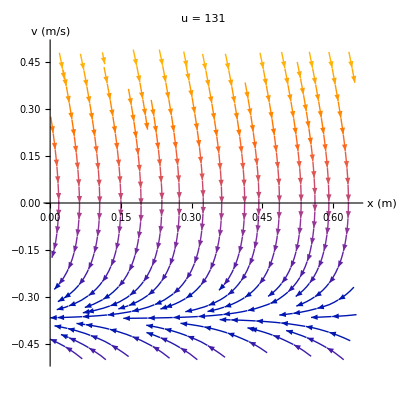

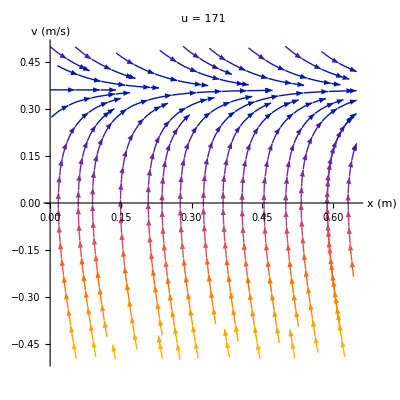

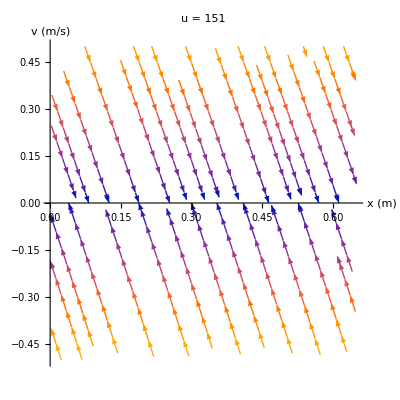

```mathematica
Clear[b,l,m,g]
g=9.81;
m=0.00283;
rho=1.225;
Cl=0.47;
r=0.02;
A=4 π r^2;
k=0.0184;
alpha=0.1885;
beta = 0.6272;
uPWMbar=((2*m*g)/(rho*A*Cl*alpha^2))^(1/(2*beta));
uPWM1= Round[uPWMbar - 20];
uPWM2 = Round[uPWMbar + 20];
plot1=StreamPlot[{x2,(0.5 rho A Cl (alpha*uPWM1^beta-x2)^2)/m-g},{x1,0,0.65},{x2,-0.5,0.5},StreamPoints->Medium,AxesOrigin->{0,0},AxesLabel->{"x (m)","v (m/s)"},Axes->True,Frame->False,AxesStyle->Directive[Black,FontSize->24],PlotLabel->"u = 131",LabelStyle->Directive[Black,FontSize->20]]
plot2=StreamPlot[{x2,(0.5 rho A Cl (alpha*uPWM2^beta-x2)^2)/m-g},{x1,0,0.65},{x2,-0.5,0.5},StreamPoints->Medium,AxesOrigin->{0,0},AxesLabel->{"x (m)","v (m/s)"},Axes->True,Frame->False,AxesStyle->Directive[Black,FontSize->24],PlotLabel->"u = 171",LabelStyle->Directive[Black,FontSize->20]]
plot3=StreamPlot[{x2,(0.5 rho A Cl (alpha*uPWMbar^beta-x2)^2)/m-g},{x1,0,0.65},{x2,-0.5,0.5},StreamPoints->Medium,AxesOrigin->{0,0},AxesLabel->{"x (m)","v (m/s)"},Axes->True,Frame->False,AxesStyle->Directive[Black,FontSize->24],PlotLabel->"u = 151",LabelStyle->Directive[Black,FontSize->20]]
```

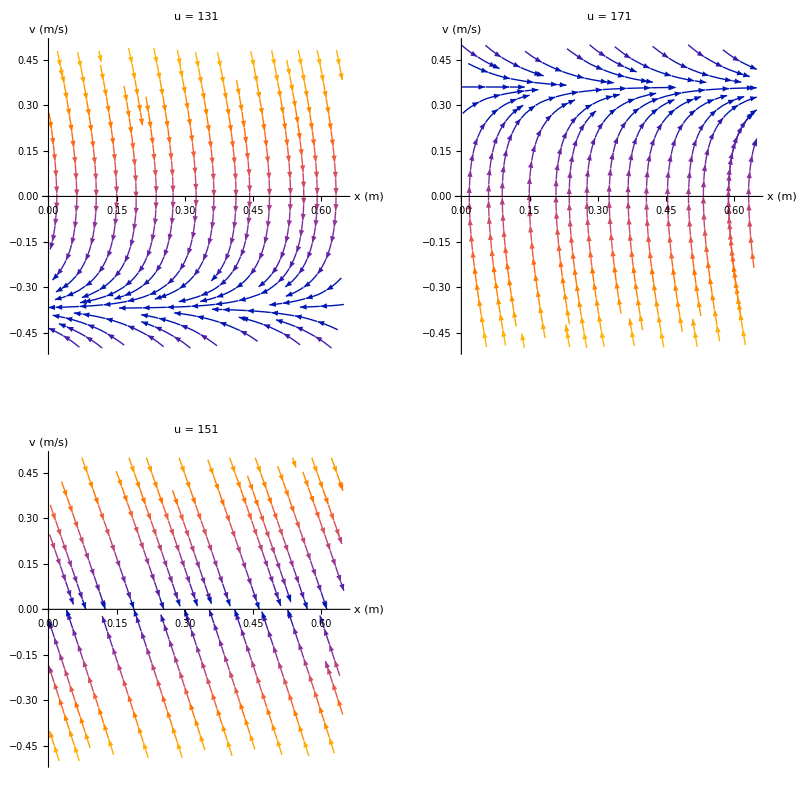

```mathematica
GraphicsGrid[{{plot1,plot2},{plot3}},ImageSize->Full]
*Manipulate[StreamPlot[{x2,0.5*rho*A*Cl*(alpha*uPWM^beta-x2)^2/m-g},{x1,0,0.65},{x2,-1,1},StreamPoints -> Fine],{uPWM,190,255}]*
```